# LTE Smoothing Program (5 Bin)

## Introduction and Instructions

#### Program Selection and Information

Use the five bin LTE Data Analysis program for most meteorites. Use the six bin LTE Data Analysis for CM2 meteorites. Using the incorrect program will not produce proper results. The input format should be a csv file with the temperature in Kelvins in the first column and the capacitance in picofarads in the second column. The output will be two files both in the format: temperature, smoothed data, derivative.  One file will have the simple derivative; the other will have the midpoint derivative.

#### Preparatory Work

The input files should be manually trimmed so that there is only cooling data. The temperature should go down to a minimum and not rebound. Error messages in the difference calculations are usually a result of stray warming data.

#### Program Instructions

1) Insert file paths for input and output files.
2) Evaluate notebook.
3) Examine plots under each bin to determine correct fits. Percent errors ought to be below 0.01% for most fits.
4) Using the midpoint derivative and derivative of lines of best fit plots as guides, adjust the list FitBoundaries under the section “Smoothed Data and Derivative.” By changing these values and then reevaluating the section “Smoothed Data and Derivative,” the gaps between the bins can be decreased or eliminated. The values should be plus or minus 5 from {35,50,75,105}.
5) Confirm files were exported successfully.

## Program

## Inputs

```mathematica
(*Enter the filepath for the input data and specify the location for the output file*)
```

```mathematica
InputFilePath= "/Users/alexwasilkoff/Desktop/OpeilLab/Smoothing/DataForThermalProcessing/Ni annealed 08nov2018.csv";
OutputFilePathSimple ="/Users/alexwasilkoff/Desktop/OpeilLab/Smoothing/ProcessedThermalData/NiAnnealed08Nov2018_sderv.csv";
OutputFilePathMid = "/Users/alexwasilkoff/Desktop/OpeilLab/Smoothing/ProcessedThermalData/NiAnnealed08Nov2018_midpt.csv";
```

## Data Import from csv File

```mathematica
Data =Import [ InputFilePath, "Data"];
```

```mathematica
ClearAll[x,y,i]
```

## Preliminary Processing

```mathematica
If[Head[Data[[1,1]]]==String,Data=Delete[Data,1]];
TempData = Data[[;;,1]];
FlooredData = Floor[TempData];
```

## Original Data

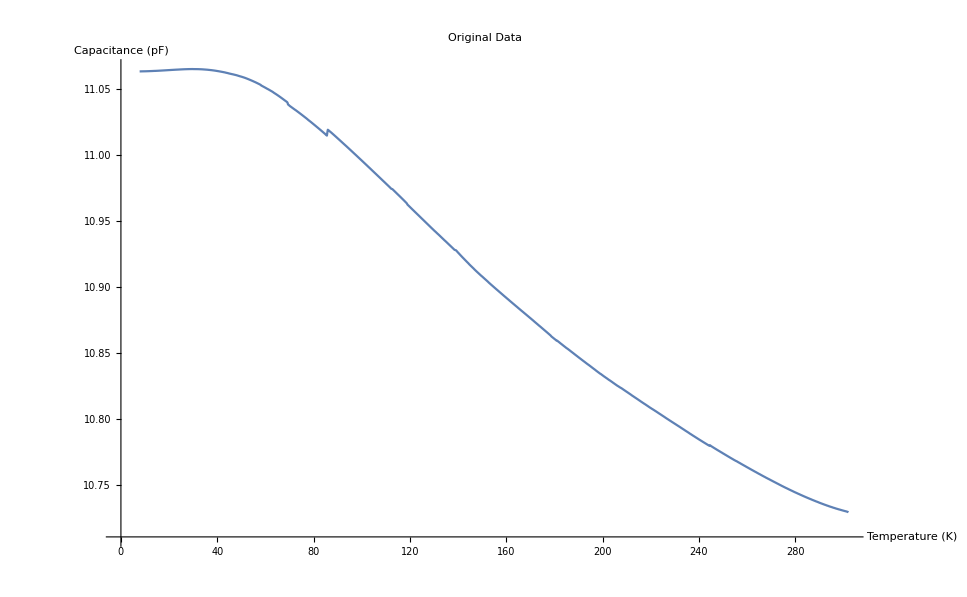

```mathematica
OriginalData = ListLinePlot[Data];
Show[OriginalData, PlotLabel->"Original Data",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

## Elimination of Discontinuities

This section finds the “step function” offset errors in the data. They are identified by calculating the difference of capacitance between adjacent points. A line of best fit is calculated, and then points which deviate from this line by a given amount are identified as outliers. The all points greater than each outlier are adjusted so that the step function phenomena are eliminated. This section is admittedly a bit rough. The cutoff points to determine outliers are basically random.

```mathematica
(*Create a table of the difference between the capacitance of adjacent points*)
```

```mathematica
DifAdjacentPoints = Table[{Data[[x,1]],Data[[x-1,2]]-Data[[x,2]]},{x,2,Length[Data]}];
```

```mathematica
(*Find a tenth order Chebyshev polynomial fit for the difference function*)
```

-0.0000882895+0.0000126945 x-1.55904×10^-7 (-1+2 x^2)-1.4265×10^-9 (-3 x+4 x^3)+3.29948×10^-11 (1-8 x^2+8 x^4)-2.42787×10^-13 (5 x-20 x^3+16 x^5)+9.63409×10^-16 (-1+18 x^2-48 x^4+32 x^6)-2.26867×10^-18 (-7 x+56 x^3-112 x^5+64 x^7)+3.17095×10^-21 (1-32 x^2+160 x^4-256 x^6+128 x^8)-2.43279×10^-24 (9 x-120 x^3+432 x^5-576 x^7+256 x^9)+7.89909×10^-28 (-1+50 x^2-400 x^4+1120 x^6-1280 x^8+512 x^10)

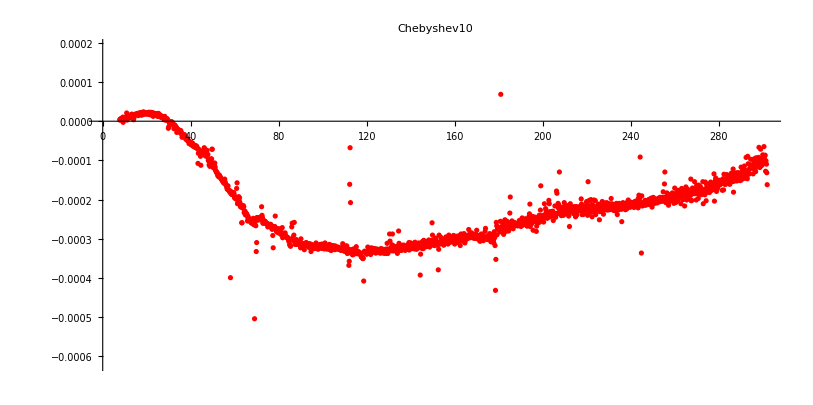

```mathematica
Chebyshev10=Fit[DifAdjacentPoints,{1,x,(2x^2-1),(4x^3-3x),(8x^4-8x^2+1),(16x^5-20x^3+5x),(32*x^6-48*x^4+18*x^2-1),(64*x^7-112*x^5+56*x^3-7*x),(128*x^8-256*x^6+160*x^4-32*x^2+1),(256*x^9-576*x^7+432*x^5-120*x^3+9x),(512*x^10-1280*x^8+1120*x^6-400*x^4+50*x^2-1)},x]
nlmCh10=NonlinearModelFit[DifAdjacentPoints,a+b*x+c*(2x^2-1)+d*(4x^3-3x)+e*(8x^4-8x^2+1)+g*(16x^5-20x^3+5x)+h*(32*x^6-48*x^4+18*x^2-1)+i*(64*x^7-112*x^5+56*x^3-7*x)+j*(128*x^8-256*x^6+160*x^4-32*x^2+1)+k*(256*x^9-576*x^7+432*x^5-120*x^3+9x)+l(512*x^10-1280*x^8+1120*x^6-400*x^4+50*x^2-1),{a,b,c,d,e,g,h,i,j,k,l},x];
InputForm[nlmCh10];
Show[ListPlot[DifAdjacentPoints,AspectRatio->0.5,PlotLabel->HoldForm[Chebyshev10],PlotStyle->Red],Plot[{Chebyshev10},{x,0,10000},PlotStyle->Blue]]
```

```mathematica
(*Find the difference between the expected difference and the actual difference*)
```

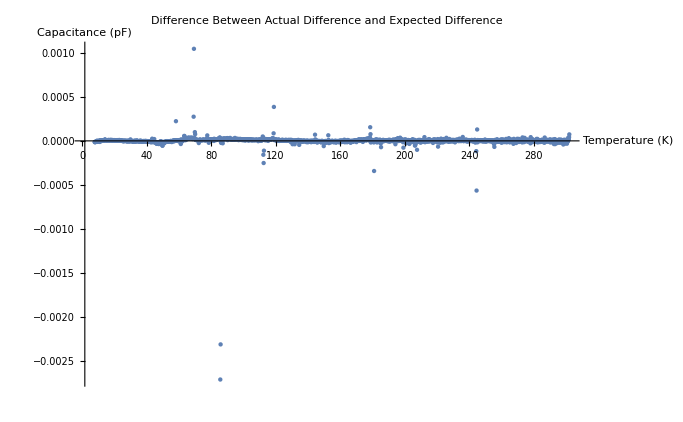

```mathematica
CalcDif =Table[{x,Chebyshev10},{x,Data[[;;,1]]}];
DifFitActual = Table[{Data[[x,1]],CalcDif[[x+1,2]] - DifAdjacentPoints[[x,2]]},{x,Length[Data]-1}];
ListPlot[DifFitActual,PlotRange->All,PlotLabel-> "Difference Between Actual Difference and Expected Difference",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

```mathematica
(*Find outliers*)
```

```mathematica
Outliers = Select[DifFitActual,Abs[#[[2]]]>0.0005&]
```

{{244.623,-0.000563382},{85.9203,-0.00230762},{85.7305,-0.00270583},{69.3891,0.00104378}}

```mathematica
(*Find the position of the outliers*)
```

```mathematica
PosOutliers = Table[Position[Data,Outliers[[x,1]]][[;;,1]],{x,Length[Outliers]}]
```

{{307},{1159},{1160},{1247}}

```mathematica
(*Two nested loops adjust the capacitance of points above outliers to remove the step function phenomena*)
```

```mathematica
Do[Do[Data = ReplacePart[Data,{PosOutliers[[i,1]]+x,2}-> Plus[Data[[PosOutliers[[i,1]]+x,2]],(-1)*Outliers[[i,2]]]],{x,0,Length[Data]-PosOutliers[[i,1]]}],{i,Length[Outliers]}]
```

```mathematica
NoStepFunctions = ListLinePlot[Data,PlotStyle->Red];
```

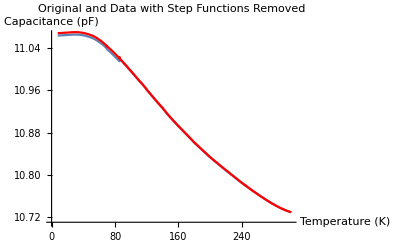

```mathematica
Show[OriginalData,NoStepFunctions,PlotLabel-> "Original and Data with Step Functions Removed",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

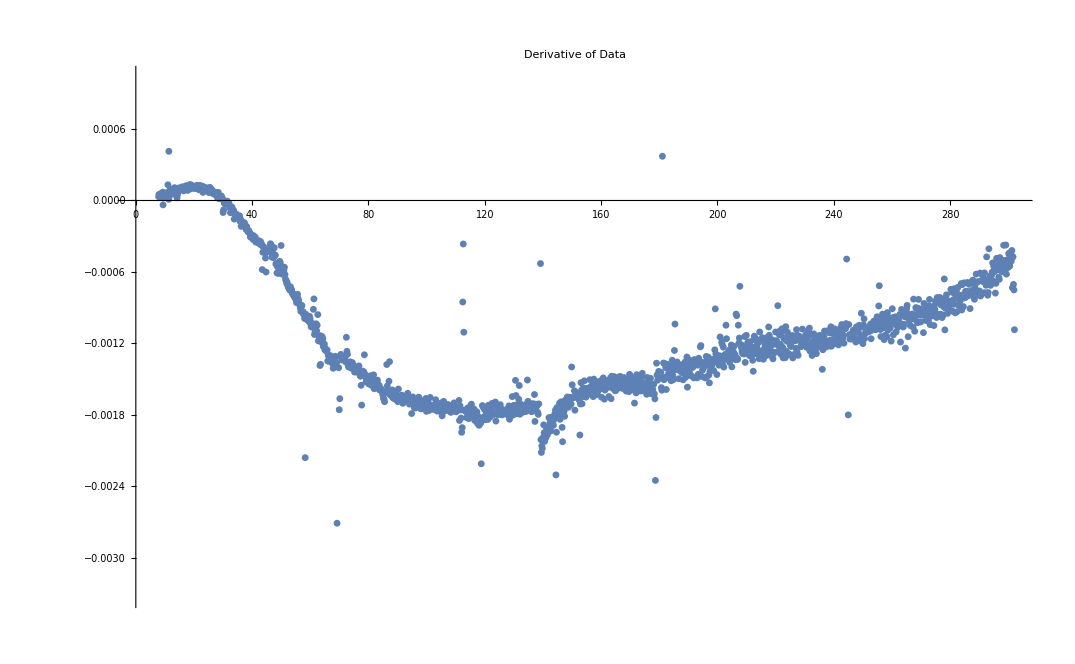

```mathematica
derData=Differences[Data]/.{x_,y_}->y/x;
derData =MapThread[{#1,#2}&,Take[#,All,Min@@Length/@#]&@{TempData,derData}];
derDataPlot=ListPlot[derData];
Show[derDataPlot,PlotLabel-> "Derivative of Data"]
```

## Bin 1 (85 K to 301 K)

The code for each bin is identical except for the appropriate data and boundaries. Thus, only Bin 1 will be annotated as an example.

### Fit

First, the appropriate points from the input dataset are selected based on the temperature boundaries. This program uses floored temperature values to identify the correct points.
Second,  a line of best fit is calculated.
Third, calculated capacitance values are generated by running the line of best fit on the original temperature data.
Finally, a plot is generated comparing the original data and the calculated data.

11.0661+0.000826498 x-0.0000165827 x^2-4.77549×10^-8 x^3+8.98533×10^-10 x^4-3.22339×10^-12 x^5+3.77665×10^-15 x^6

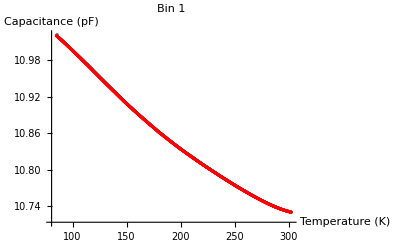

```mathematica
Bin1 = Data[[;;Max[Position[FlooredData,85]]]];
p1 = ListPlot[Bin1];
line1 = Fit[Bin1, {1,x,x^2,x^3,x^4,x^5,x^6},x]
CapCalc1 = Table[{x,line1},{x,Bin1[[;;,1]]}];
p2 = ListPlot[CapCalc1,PlotStyle->Red];
Show[p1,p2,PlotLabel->"Bin 1",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

### Error Analysis

Error is calculated by finding the difference between the original data and the calculated capacitance. This is converted into a percentage and then graphed.

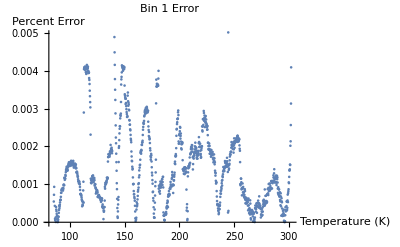

```mathematica
Dif1 = Bin1[[;;]]-CapCalc1[[;;]];
PercentError1 = Table[{Bin1[[x,1]],Abs[Dif1[[x,2]]/Bin1[[x,2]]*100]},{x,Length[Bin1]}];
ListPlot[PercentError1,PlotLabel->"Bin 1 Error",AxesLabel->{"Temperature (K)","Percent Error"}]
```

## Bin 2 (65 K to 115 K)

### Fit

11.2665-0.0082333 x+0.000134567 x^2-1.12823×10^-6 x^3+3.35837×10^-9 x^4

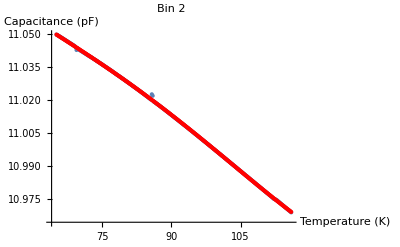

```mathematica
Bin2 = Data[[Min[Position[FlooredData, 115]];;Max[Position[FlooredData,65]]]];
p1 = ListPlot[Bin2];
line2 = Fit[Bin2, {1,x,x^2,x^3,x^4},x]
CapCalc2 = Table[{x,line2},{x,Bin2[[;;,1]]}];
p2 = ListPlot[CapCalc2,PlotStyle->Red];
Show[p1,p2,PlotLabel->"Bin 2",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

### Error Analysis

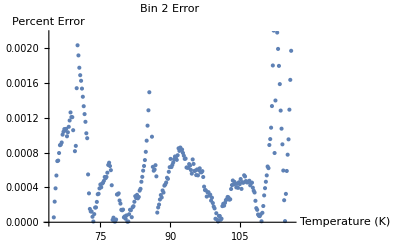

```mathematica
Dif2 = Bin2[[;;]]-CapCalc2[[;;]];
PercentError2 = Table[{Bin2[[x,1]],Abs[Dif2[[x,2]]/Bin2[[x,2]]*100]},{x,Length[Bin2]}];
ListPlot[PercentError2,PlotLabel->"Bin 2 Error",AxesLabel->{"Temperature (K)","Percent Error"}]
```

## Bin 3 (45 K to 85 K)

### Fit

11.1026-0.0052486 x+0.00024557 x^2-4.85348×10^-6 x^3+4.11444×10^-8 x^4-1.29936×10^-10 x^5

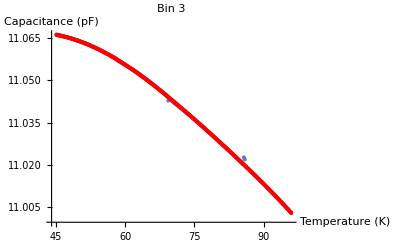

```mathematica
Bin3 = Data[[Min[Position[FlooredData, 95]];;Max[Position[FlooredData,45]]]];
p1 = ListPlot[Bin3];
line3 = Fit[Bin3, {1,x,x^2,x^3,x^4,x^5},x]
CapCalc3 = Table[{x,line3},{x,Bin3[[;;,1]]}];
p2 = ListPlot[CapCalc3,PlotStyle->Red];
Show[p1,p2,PlotLabel->"Bin 3",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

### Error Analysis

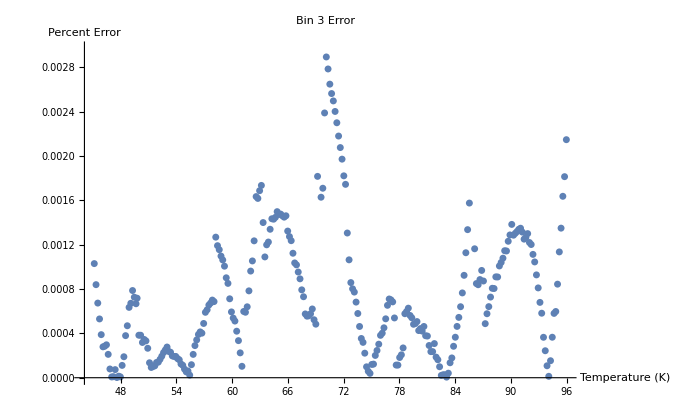

```mathematica
Dif3 = Bin3[[;;]]-CapCalc3[[;;]];
PercentError3 = Table[{Bin3[[x,1]],Abs[Dif3[[x,2]]/Bin3[[x,2]]*100]},{x,Length[Bin3]}];
ListPlot[PercentError3,PlotLabel->"Bin 3 Error",AxesLabel->{"Temperature (K)","Percent Error"}]
```

## Bin 4 (30 K to 55 K)

### Fit

11.1651-0.0134843 x+0.000734808 x^2-0.0000192898 x^3+2.44912×10^-7 x^4-1.2272×10^-9 x^5

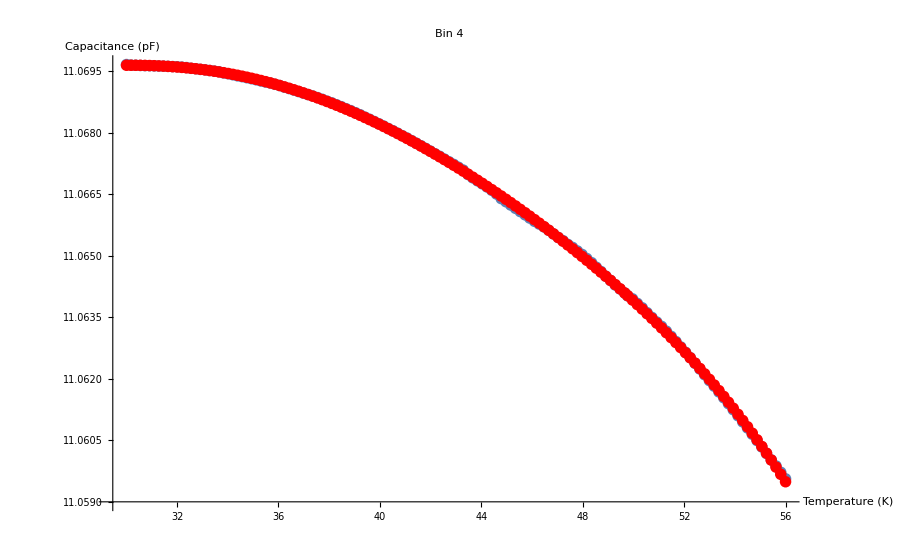

```mathematica
Bin4 = Data[[Min[Position[FlooredData, 55]];;Max[Position[FlooredData,30]]]];
p1 = ListPlot[Bin4];
line4 = Fit[Bin4, {1,x,x^2,x^3,x^4,x^5},x]
CapCalc4 = Table[{x,line4},{x,Bin4[[;;,1]]}];
p2 = ListPlot[CapCalc4,PlotStyle->Red];
Show[p1,p2,PlotLabel->"Bin 4",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

### Error Analysis

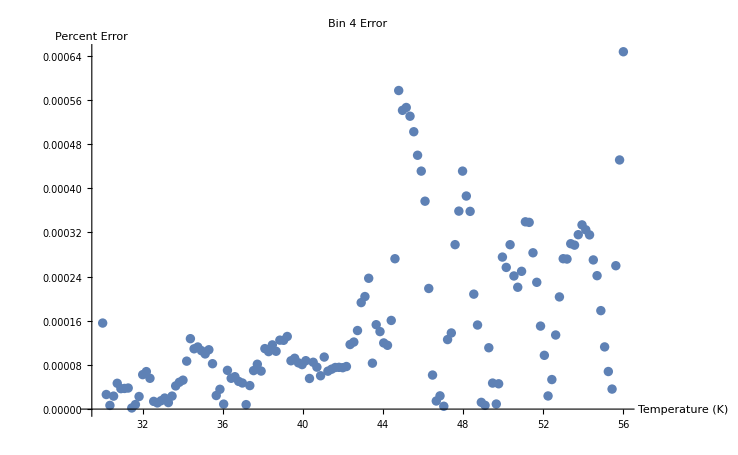

```mathematica
Dif4 = Bin4[[;;]]-CapCalc4[[;;]];
PercentError4 = Table[{Bin4[[x,1]],Abs[Dif4[[x,2]]/Bin4[[x,2]]*100]},{x,Length[Bin4]}];
ListPlot[PercentError4,PlotLabel->"Bin 4 Error",AxesLabel->{"Temperature (K)","Percent Error"}]
```

## Bin 5 (40 K and below)

### Fit

11.0677+0.0000456694 x-5.25002×10^-6 x^2+4.64983×10^-7 x^3-4.51467×10^-9 x^4-2.59776×10^-10 x^5+3.78696×10^-12 x^6

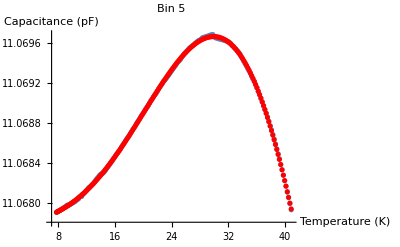

```mathematica
Bin5 = Data[[Min[Position[FlooredData, 40]];;]];
p1 = ListPlot[Bin5];
line5 = Fit[Bin5, {1,x,x^2,x^3,x^4,x^5,x^6},x]
CapCalc5 = Table[{x,line5},{x,Bin5[[;;,1]]}];
p2 = ListPlot[CapCalc5,PlotStyle->Red];
Show[p1,p2,PlotLabel->"Bin 5",AxesLabel->{"Temperature (K)","Capacitance (pF)"}]
```

### Error Analysis

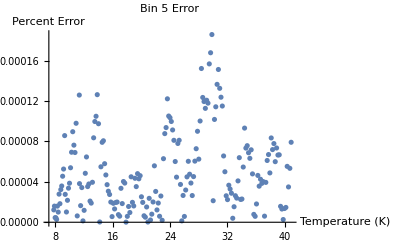

```mathematica
Dif5 = Bin5[[;;]]-CapCalc5[[;;]];
PercentError5 = Table[{Bin5[[x,1]],Abs[Dif5[[x,2]]/Bin5[[x,2]]*100]},{x,Length[Bin5]}];
ListPlot[PercentError5,PlotLabel->"Bin 5 Error",AxesLabel->{"Temperature (K)","Percent Error"}]
```

## Lines of Best Fit

The various lines of best fit are printed together with their temperature boundaries.

```mathematica
Print["For 301 K to 100 K: ",line1];Print["For 100 K to 75 K: ", line2];Print["For 75 K to 50 K: ",line3];Print["For 50 K to 35 K: ",line4];
Print["For 35 K and below: ", line5];
```

For 301 K to 100 K: 11.0661+0.000826498 x-0.0000165827 x^2-4.77549×10^-8 x^3+8.98533×10^-10 x^4-3.22339×10^-12 x^5+3.77665×10^-15 x^6

For 100 K to 75 K: 11.2665-0.0082333 x+0.000134567 x^2-1.12823×10^-6 x^3+3.35837×10^-9 x^4

For 75 K to 50 K: 11.1026-0.0052486 x+0.00024557 x^2-4.85348×10^-6 x^3+4.11444×10^-8 x^4-1.29936×10^-10 x^5

For 50 K to 35 K: 11.1651-0.0134843 x+0.000734808 x^2-0.0000192898 x^3+2.44912×10^-7 x^4-1.2272×10^-9 x^5

For 35 K and below: 11.0677+0.0000456694 x-5.25002×10^-6 x^2+4.64983×10^-7 x^3-4.51467×10^-9 x^4-2.59776×10^-10 x^5+3.78696×10^-12 x^6

## Derivatives of Lines of Best Fit

The derivatives of the lines of best fit are calculated, and then graphed in their appropriate temperature range. The discontinuities in the derivatives are concerning.

```mathematica
Deriv1 = D[line1,x]
```

0.000826498-0.0000331655 x-1.43265×10^-7 x^2+3.59413×10^-9 x^3-1.6117×10^-11 x^4+2.26599×10^-14 x^5

```mathematica
Deriv2 = D[line2,x]
```

-0.0082333+0.000269134 x-3.38469×10^-6 x^2+1.34335×10^-8 x^3

```mathematica
Deriv3 = D[line3,x]
```

-0.0052486+0.000491141 x-0.0000145605 x^2+1.64578×10^-7 x^3-6.49682×10^-10 x^4

```mathematica
Deriv4 = D[line4,x]
```

-0.0134843+0.00146962 x-0.0000578693 x^2+9.79647×10^-7 x^3-6.13602×10^-9 x^4

```mathematica
Deriv5 = D[line5,x]
```

0.0000456694-0.0000105 x+1.39495×10^-6 x^2-1.80587×10^-8 x^3-1.29888×10^-9 x^4+2.27217×10^-11 x^5

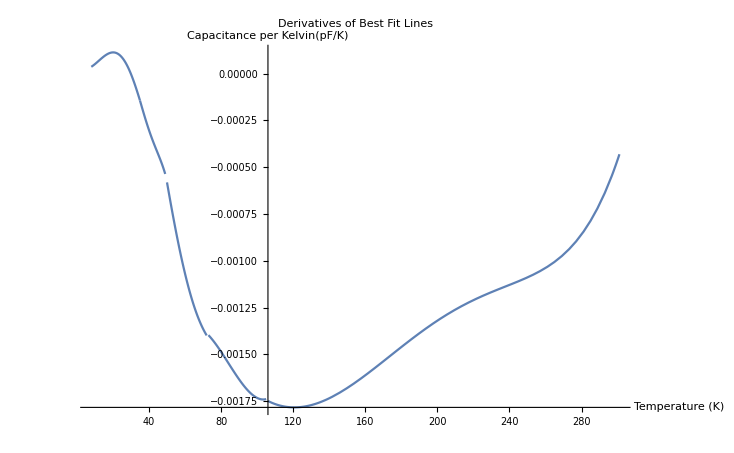

```mathematica
p1 =Plot[Deriv1,{x,106,301}];
p2 =Plot[Deriv2,{x,73,105}];
p3 =Plot[Deriv3,{x,50,72}];
p4=Plot[Deriv4,{x,35,49}];
p5=Plot[Deriv5,{x,8,35}];
Show[p1,p2,p3,p4,p5,PlotRange-> All,PlotLabel-> "Derivatives of Best Fit Lines",AxesLabel->{"Temperature (K)","Capacitance per Kelvin(pF/K)"}]
```

## Smoothed Data and Derivative

```mathematica
FitBoundaries={39,50,73,103};
```

### Trim Bins

```mathematica
CapCalc1Clipped = CapCalc1[[;;Position[Floor[CapCalc1],FitBoundaries[[-1]]][[-1,1]]]];
CapCalc2Clipped = CapCalc2[[Position[Floor[CapCalc2],FitBoundaries[[-1]]-1][[1,1]];;Position[Floor[CapCalc2],FitBoundaries[[-2]]][[-1,1]]]];
CapCalc3Clipped = CapCalc3[[Position[Floor[CapCalc3],FitBoundaries[[-2]]-1][[1,1]];;Position[Floor[CapCalc3],FitBoundaries[[-3]]][[-1,1]]]];
CapCalc4Clipped = CapCalc4[[Position[Floor[CapCalc4],FitBoundaries[[-3]]-1][[1,1]];;Position[Floor[CapCalc4],FitBoundaries[[-4]]][[-1,1]]]];
CapCalc5Clipped = CapCalc5[[Position[Floor[CapCalc5],FitBoundaries[[-4]]-1][[1,1]];;]];
```

### Join Bins

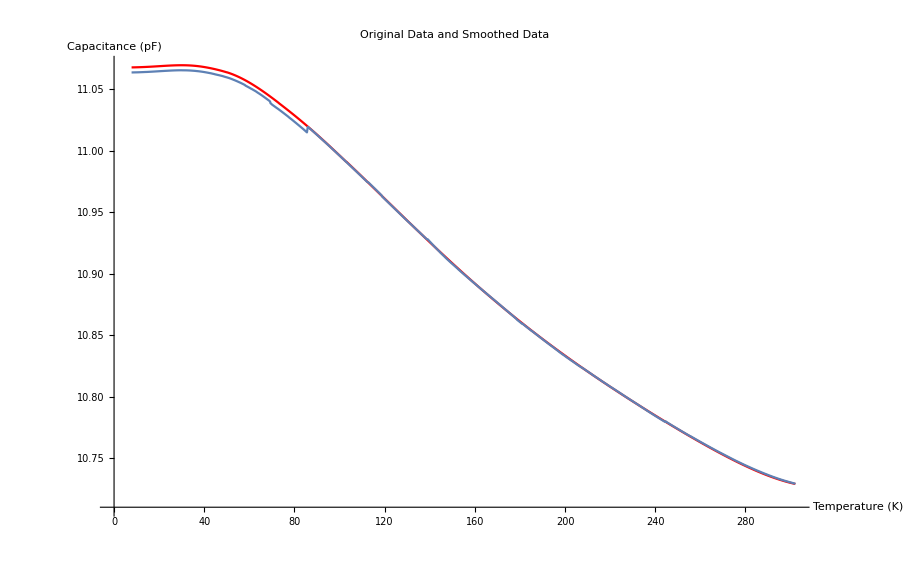

```mathematica
SmoothedData = Join[CapCalc1Clipped,CapCalc2Clipped,CapCalc3Clipped,CapCalc4Clipped,CapCalc5Clipped];
(*The smoothed data is adjusted so that the highest temperature's capacitance is the same in the smoothed and original data*)
HighestTempDifference = SmoothedData[[1,2]]-Data[[1,2]];
SmoothedData = Table[{SmoothedData[[x,1]],SmoothedData[[x,2]]-HighestTempDifference},{x,Length[SmoothedData]}];
SmoothedDataGraph = ListLinePlot[SmoothedData, PlotStyle->Red];
Show[SmoothedDataGraph,OriginalData,PlotLabel-> "Original Data and Smoothed Data",AxesLabel->{"Temperature (K)","Capacitance (pF)"},PlotLegends-> LineLegend[{Red,Blue},{"Smoothed Data","Original Data"}]]
```

### Eliminate Outliers

```mathematica
BinOutliersPos =Table[Max[Position[FlooredData,x]],{x,FitBoundaries}];
Do[SmoothedData[[x]]={0,0},{x,BinOutliersPos}];
SmoothedData = DeleteCases[SmoothedData,{0,0}];
```

```mathematica
TempBinOutliersPos =Table[Max[Position[FlooredData,x]],{x,FitBoundaries}];
Do[TempData[[x]]={0},{x,TempBinOutliersPos}];
TempData=DeleteCases[TempData,{0}];
```

### Calculate Derivative

```mathematica
SmoothCap= SmoothedData[[;;,2]];
```

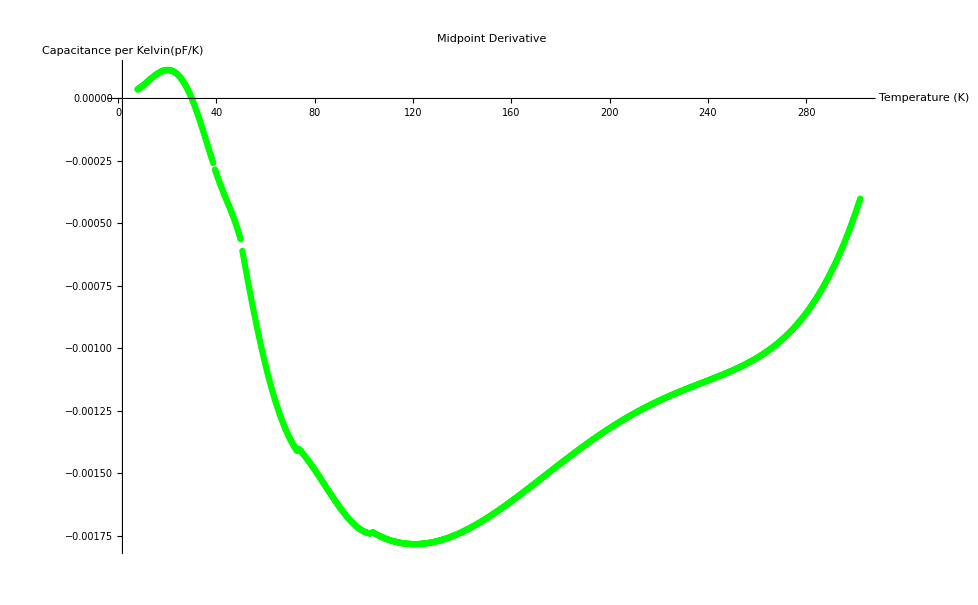

```mathematica
derSmoothedMid=Table[0.5(((SmoothCap[[x+1]]-SmoothCap[[x]])/(TempData[[x+1]]-TempData[[x]]))+((SmoothCap[[x]]-SmoothCap[[x-1]])/(TempData[[x]]-TempData[[x-1]]))),{x,2,Length[SmoothedData]-1}];
derSmoothedMid=Table[{TempData[[x+1]],derSmoothedMid[[x]]},{x,Length[SmoothedData]-2}];BinOutliersPos =Table[Max[Position[Floor[derSmoothedMid],x]],{x,FitBoundaries}];
Do[derSmoothedMid[[x+1]]={0,0},{x,BinOutliersPos}];
Do[derSmoothedMid[[x]]={0,0},{x,BinOutliersPos}];
derSmoothedMid = DeleteCases[derSmoothedMid,{0,0}];
derSmoothedMidPlot=ListPlot[derSmoothedMid,PlotStyle->Green,PlotLabel->"Midpoint Derivative",AxesLabel->{"Temperature (K)","Capacitance per Kelvin(pF/K)"},PlotRange->All]
```

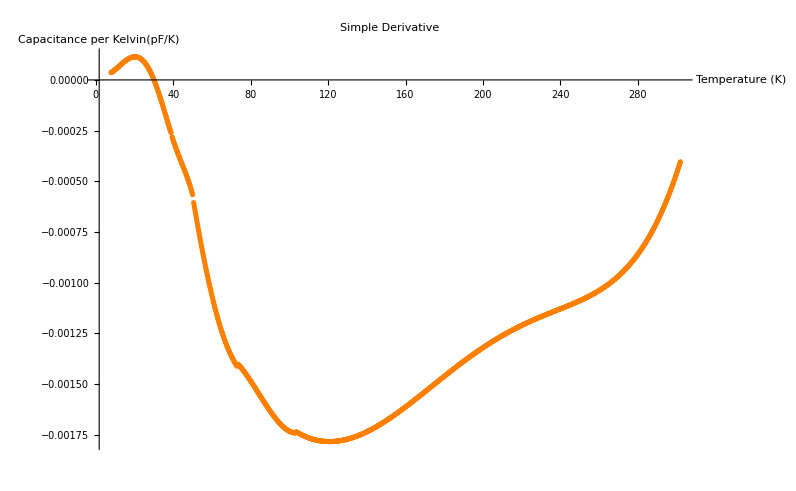

```mathematica
derSmoothedSimple=Evaluate[Differences[SmoothedData]]/.{x_,y_}->Evaluate[y/x];
derSmoothedSimple =MapThread[{#1,#2}&,Take[#,All,Min@@Length/@#]&@{TempData,derSmoothedSimple}];
derSmoothedSimple=Drop[derSmoothedSimple,1];BinOutliersPos =Table[Max[Position[Floor[derSmoothedSimple],x]],{x,FitBoundaries}];
Do[derSmoothedSimple[[x]]={0,0},{x,BinOutliersPos}];
derSmoothedSimple = DeleteCases[derSmoothedSimple,{0,0}];
derSmoothedSimplePlot= ListPlot[derSmoothedSimple,PlotStyle->Orange,PlotLabel->"Simple Derivative",AxesLabel->{"Temperature (K)","Capacitance per Kelvin(pF/K)"},PlotRange->Full]
```

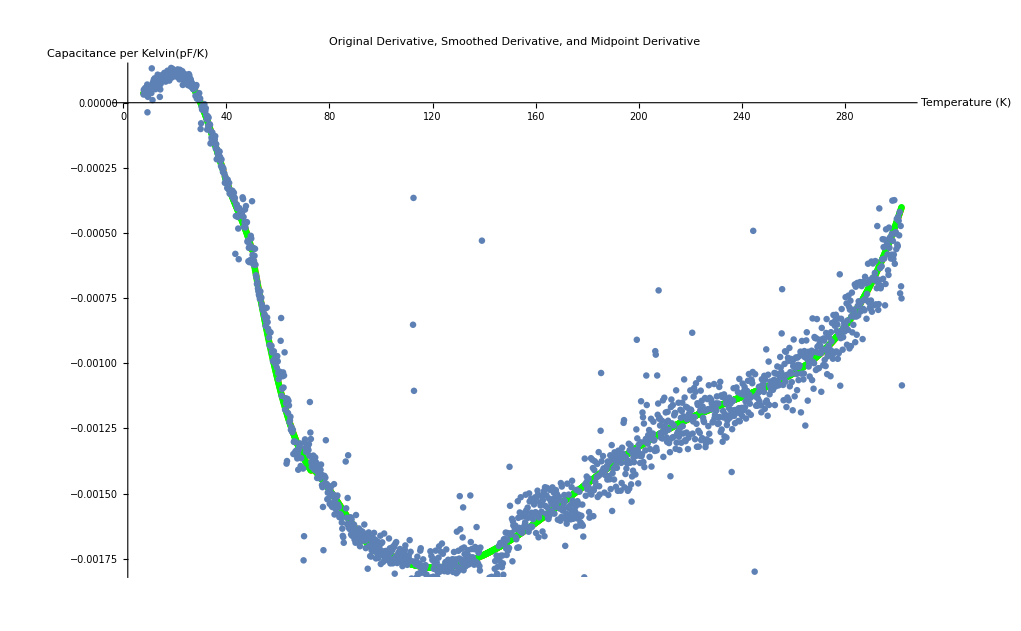

```mathematica
Show[derSmoothedSimplePlot,derSmoothedMidPlot,derDataPlot,PlotLabel-> "Original Derivative, Smoothed Derivative, and Midpoint Derivative",AxesLabel->{"Temperature (K)","Capacitance per Kelvin(pF/K)"}]
```

## Export

```mathematica
(*Collect all pertinent data into the two lists*)
```

```mathematica
SimpleData = Table[{SmoothedData[[i,1]],SmoothedData[[i,2]],derSmoothedSimple[[i,2]]},{i,Length[derSmoothedSimple]}];
```

```mathematica
MidData = Table[{SmoothedData[[i,1]],SmoothedData[[i,2]],derSmoothedMid[[i,2]]},{i,Length[derSmoothedMid]}];
```

```mathematica
(*The temperature values are truncated to three decimal places*)
```

```mathematica
FinalDataTemp3Simple=Table[{NumberForm[SimpleData[[x,1]],{Infinity,3}],SimpleData[[x,2]],SimpleData[[x,3]]},{x,Length[SimpleData]}];
```

```mathematica
FinalDataTemp3Mid=Table[{NumberForm[MidData[[x,1]],{Infinity,3}],MidData[[x,2]],MidData[[x,3]]},{x,Length[MidData]}];
```

```mathematica
(*Name the Columns*)
FinalDataExportSimple=Prepend[FinalDataTemp3Simple,{"Temperature(K)","Capacitance(pF)","Simple Derivative(pF/K)"}];
```

```mathematica
FinalDataExportMid=Prepend[FinalDataTemp3Mid,{"Temperature(K)","Capacitance(pF)","Midpoint Derivative(pF/K)"}];
```

```mathematica
(*The smoothed data is exported as a csv file*)
```

```mathematica
Export[OutputFilePathSimple,FinalDataExportSimple];
```

```mathematica
Export[OutputFilePathMid,FinalDataExportMid];
```